## Brian — PS 8 — 2025-02-18 — Solution

## EIWL3 Sections 20, 21, and 22

## Exercises from EIWL3 Section 20

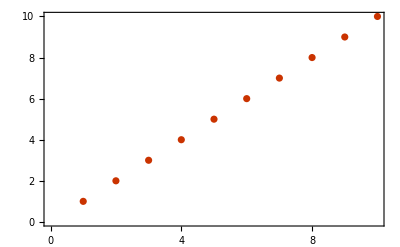

```mathematica
(* 20.1 *) ListPlot[Range[10], PlotTheme->"Web"]
```

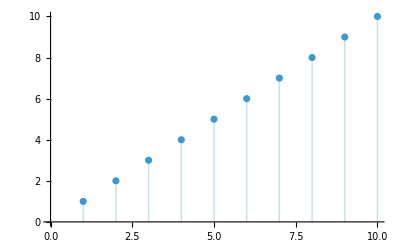

```mathematica
(* 20.2 *) ListPlot[Range[10],Filling->Axis]
(* That is interesting filling. I wonder if *)
(* Wolfram wanted a list line plot. *)
```

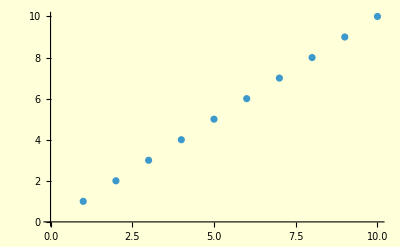

```mathematica
(* 20.3 *) ListPlot[Range[10],Background->LightYellow]
(* I couldn't bear the bright yellow so I dimmed it. *)
```

```mathematica
(* 20.4 *) GeoListPlot[Entity["Country","Australia"],GeoRange->All]
```

-Graphics-

```mathematica
(* 20.5 *) GeoListPlot[Entity["Country","Madagascar"],GeoRange->Entity["Ocean","IndianOcean"]]
```

-Graphics-

```mathematica
(* 20.6 *) GeoGraphics[EntityClass["Country","SouthAmerica"],GeoBackground->"ReliefMap"]
```

-Graphics-

```mathematica
(* 20.7 *) GeoListPlot[{,Entity["Country","Finland"],},GeoRange->Entity["GeographicRegion","Europe"],GeoLabels->True]
```

-Graphics-

```mathematica
(* 20.8 *) GeoListPlot[EntityClass["University","TheIvyLeague"],GeoLabels->True]
```

-Graphics-

```mathematica
(* 20.9 *)Style[Grid[ Table[x y,{x,12},{y,12} ],Background->Black],White]
(* Is this the way we were meant to solve this? Well it works. *)
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
(* 20.10 *) Table[Graphics[Disk[],ImageSize->RandomInteger[{1,40}]],100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

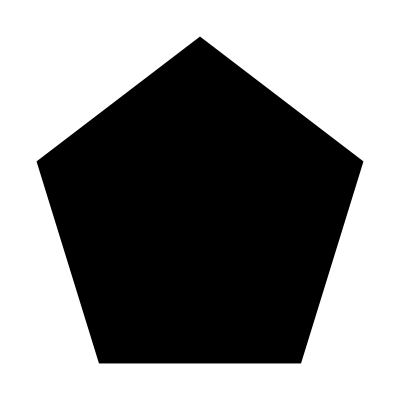
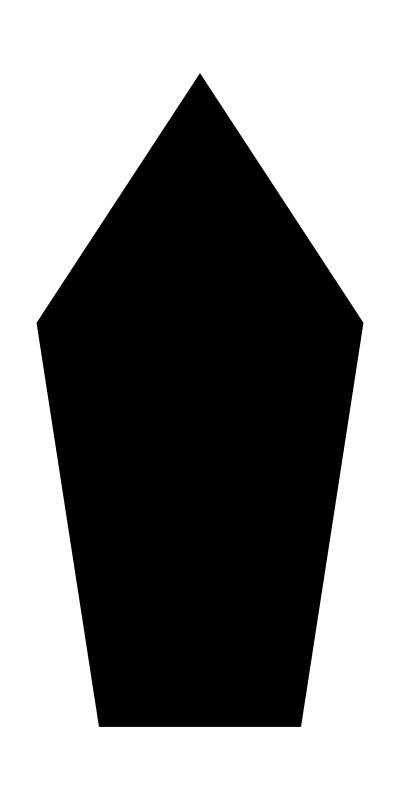
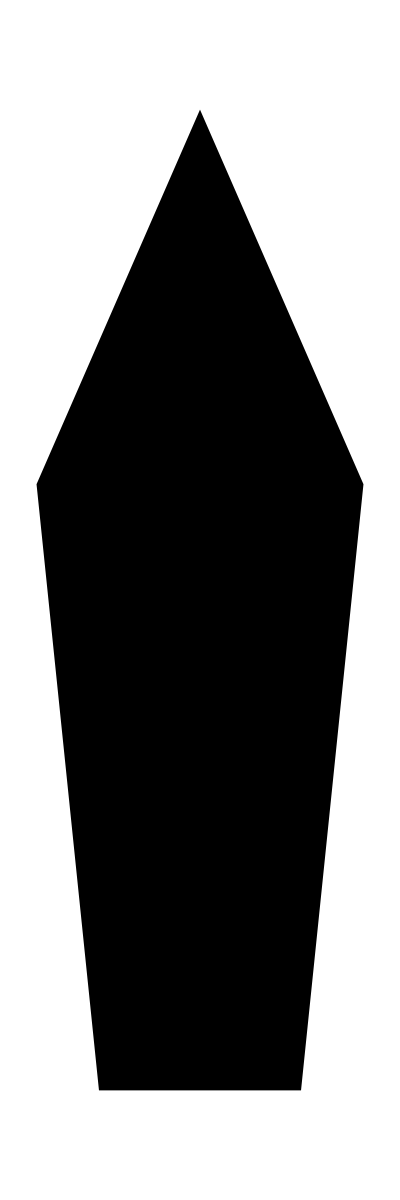
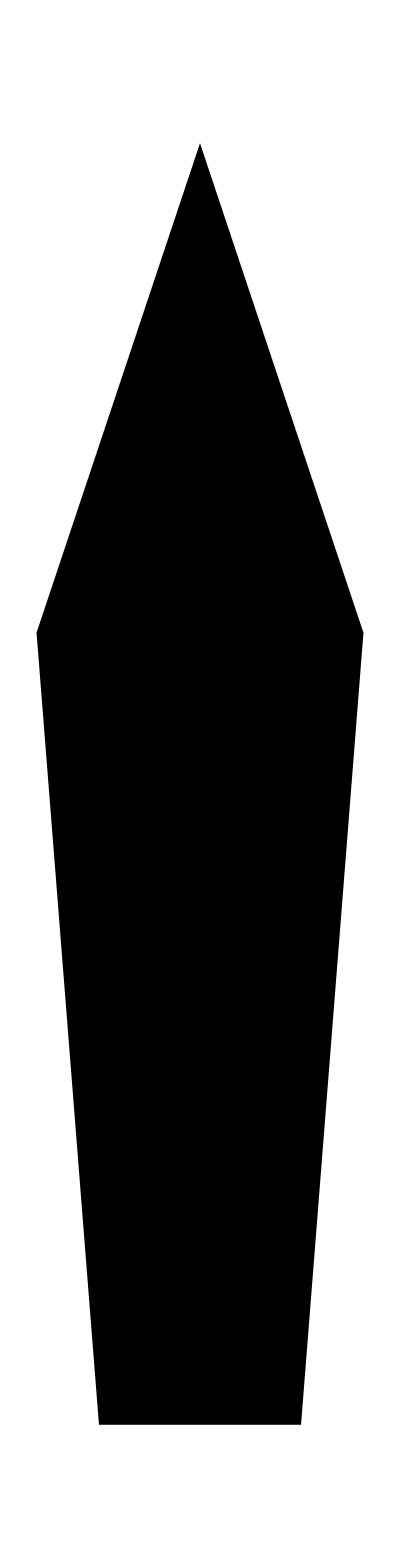
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 20.11 *) Table[Graphics[RegularPolygon[5],AspectRatio->aspectRatio],{aspectRatio,1,10}]
```

```mathematica
(* 20.12 *) Manipulate[Graphics[Circle[],ImageSize->size],{size,5,500}]
```

```mathematica
(* 20.13 *) Grid[Table[RandomColor[],{i,10},{j,10}],Frame->All]
```

RGBColor[0.19302628443945458, 0.6943482596750667, 0.715857738196269] | RGBColor[0.959571424057907, 0.16949963349581476, 0.0001164243899436368] | RGBColor[0.13528534511112156, 0.9296651119459232, 0.10787510089475227] | RGBColor[0.6202961766381447, 0.9080051132941647, 0.4906692071826704] | RGBColor[0.6075043407248268, 0.20580165839348674, 0.4433645388616323] | RGBColor[0.13217655560772434, 0.5596233054401922, 0.18893127808853039] | RGBColor[0.9039678379041836, 0.24423535600579305, 0.7401619909928083] | RGBColor[0.6378190073647643, 0.5392381280708907, 0.022864046500245427] | RGBColor[0.987008451618619, 0.7526457603064594, 0.5942815562542509] | RGBColor[0.48768023698393126, 0.022975880779740887, 0.21504888858137594]
RGBColor[0.2125362471347536, 0.05684302377703787, 0.6170392791337105] | RGBColor[0.8417079004513066, 0.9795353083877112, 0.821604898049594] | RGBColor[0.5369460177501426, 0.8989355154357652, 0.4604877302340378] | RGBColor[0.755729240053777, 0.09759708669176992, 0.004299629308544439] | RGBColor[0.8751880889063666, 0.4281157571658869, 0.7836324538832764] | RGBColor[0.534377064962164, 0.12793424765351968, 0.38910569372717907] | RGBColor[0.7118660054318453, 0.17892428739372268, 0.5764703446277266] | RGBColor[0.1611901788356349, 0.7292268931799268, 0.796401921483338] | RGBColor[0.839908303141542, 0.7331770474593493, 0.6462182541482271] | RGBColor[0.6755764972032614, 0.5601104855913452, 0.16165226118413112]
RGBColor[0.35447043077011475, 0.35200266330088636, 0.6544705486389786] | RGBColor[0.7996992987318343, 0.4066736350907749, 0.8920701833231885] | RGBColor[0.5288308179363226, 0.9161147524768518, 0.8407878812830758] | RGBColor[0.22946860817471282, 0.5436769496477785, 0.9705305429836972] | RGBColor[0.6347094149157855, 0.6329839804974302, 0.40673325790809156] | RGBColor[0.90462108882235, 0.7218334847288024, 0.11480175344887811] | RGBColor[0.7052075925240495, 0.17199323469408778, 0.9508763176940374] | RGBColor[0.7451900437435579, 0.8085584745209808, 0.9496853502680969] | RGBColor[0.5291077893807474, 0.12577622285756496, 0.8877730373739152] | RGBColor[0.9498162980566447, 0.8882913966548436, 0.013653429696197428]
RGBColor[0.6791992036040777, 0.3307571075784317, 0.10703048341873966] | RGBColor[0.4459406396434389, 0.5108252305444307, 0.4971986853188457] | RGBColor[0.4525515481870277, 0.8437316731036895, 0.035125378730325396] | RGBColor[0.6758059135259409, 0.47416541568792425, 0.41746147547314316] | RGBColor[0.568412515357692, 0.051667190333597235, 0.9772656444234988] | RGBColor[0.6133592019376681, 0.7815993807820476, 0.6436389584109548] | RGBColor[0.1553928427125908, 0.485883579087496, 0.44898966364829973] | RGBColor[0.3589749523870218, 0.1961734861954174, 0.30991947008912035] | RGBColor[0.9639059111172592, 0.10452283000252471, 0.18872092455690948] | RGBColor[0.6625237924815528, 0.10371206992303139, 0.21259621206894952]
RGBColor[0.2163025532258942, 0.618667322805021, 0.8304216647340168] | RGBColor[0.4679851005498272, 0.4863210524471844, 0.2693672814790411] | RGBColor[0.3164052394440713, 0.4002685591576509, 0.02240909506209743] | RGBColor[0.9716379209894448, 0.9209355520971036, 0.02321933764738171] | RGBColor[0.5302443662055787, 0.5611032143352745, 0.6553796411077817] | RGBColor[0.3710374807861063, 0.5063893166506612, 0.9269797729969029] | RGBColor[0.19435198532374387, 0.9475370043236475, 0.6294441037174026] | RGBColor[0.21500709156485098, 0.37013234774888715, 0.4422640657696981] | RGBColor[0.617134315360913, 0.8894012291675835, 0.8624948318736005] | RGBColor[0.9590688588737937, 0.9194810504383075, 0.5069786621845247]
RGBColor[0.7014871417229336, 0.9113747694603263, 0.9619566914342017] | RGBColor[0.7246155223419115, 0.19290960806959445, 0.9784486224734907] | RGBColor[0.9755133801250029, 0.39707366208802797, 0.14915133762395616] | RGBColor[0.7421489600770297, 0.7748298995696223, 0.29728016341426233] | RGBColor[0.4519648576169726, 0.4642629667388063, 0.18725135517244573] | RGBColor[0.7446507677725178, 0.3520912324772727, 0.653253264269867] | RGBColor[0.8583606970187616, 0.1957683393551315, 0.381306736004819] | RGBColor[0.6344435877478938, 0.8252639243052053, 0.6520330181454774] | RGBColor[0.567523082291042, 0.07673424060749445, 0.5214760364246143] | RGBColor[0.4154388049610547, 0.013404136463511573, 0.7330405516855678]
RGBColor[0.44487017441330146, 0.3985435851197703, 0.5063211180527762] | RGBColor[0.06609334478100104, 0.4140657434764188, 0.36183485809210825] | RGBColor[0.6544001427859814, 0.048401798018427256, 0.06423146528912538] | RGBColor[0.715777974659789, 0.05829910095861446, 0.019548684750158474] | RGBColor[0.9525478575394111, 0.77188161038207, 0.47376508665847816] | RGBColor[0.5661149904909692, 0.8969089180058198, 0.0750890919932723] | RGBColor[0.2764302480836711, 0.38709979131026806, 0.8611264167308825] | RGBColor[0.5452044674620717, 0.4625133876022307, 0.019123824181277227] | RGBColor[0.38349697965969054, 0.7617757254738216, 0.10488935774685704] | RGBColor[0.14787038802953312, 0.4307117715352582, 0.20644152983553243]
RGBColor[0.9947511302109695, 0.5046932877123009, 0.5419799489252071] | RGBColor[0.3833822552913362, 0.530033898613506, 0.6231183259713287] | RGBColor[0.6549629474016327, 0.15183036124477867, 0.2762465653741646] | RGBColor[0.7760372281474435, 0.03846815621071564, 0.638898191380687] | RGBColor[0.6007615294270916, 0.8330486651261788, 0.9880035560920715] | RGBColor[0.8581830136392101, 0.9441165490842678, 0.19067117765929864] | RGBColor[0.22561297193148278, 0.3225319849122903, 0.8580024776895403] | RGBColor[0.4774496524625391, 0.6540616614076153, 0.8328695237905632] | RGBColor[0.7830502854016435, 0.332898032579626, 0.6634084542845233] | RGBColor[0.599530514459877, 0.9187879454142265, 0.15902180876812255]
RGBColor[0.5443322718325763, 0.5689231352826791, 0.15440881292630304] | RGBColor[0.18804896525520953, 0.8935469343554252, 0.6745420970442697] | RGBColor[0.007183410436764293, 0.5541358685684037, 0.2622183740478472] | RGBColor[0.8159633733402669, 0.6598178155639927, 0.8312871793847902] | RGBColor[0.8374763991663412, 0.8739275032265299, 0.7213408348054611] | RGBColor[0.6775608284183776, 0.9072276102681858, 0.678042118315644] | RGBColor[0.04433231650571745, 0.46170232128225996, 0.47480527713433607] | RGBColor[0.17683846760468813, 0.16493507411872232, 0.10605519800384422] | RGBColor[0.7178501104676613, 0.1502551578650302, 0.9060099131001089] | RGBColor[0.08461526647064987, 0.4674172314676226, 0.9317041279213596]
RGBColor[0.3640082738123591, 0.04544568960489337, 0.5269258688322875] | RGBColor[0.2774544068879736, 0.8341085585670118, 0.2823752918036182] | RGBColor[0.7787195353402998, 0.88428621161046, 0.6654744869463056] | RGBColor[0.19503277975219113, 0.45779196714787607, 0.983859594096435] | RGBColor[0.18406149228281143, 0.7508679167515255, 0.3745241421479444] | RGBColor[0.720210257508018, 0.1460257834843619, 0.9243295667304232] | RGBColor[0.8250619150604397, 0.13396048665850446, 0.4163537184280446] | RGBColor[0.8643550473594805, 0.2538508383289759, 0.40804267614292633] | RGBColor[0.9498198420859727, 0.9386888532901561, 0.11132187170812102] | RGBColor[0.9934795765670901, 0.6262772803929249, 0.9586404500498458]

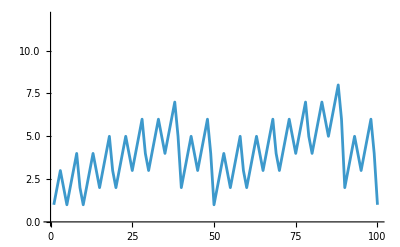

```mathematica
(* 20.24 *) ListLinePlot[
Table[StringLength[RomanNumeral[i]],{i,100}],
PlotRange->Max[Table[StringLength[RomanNumeral[i]],{i,1000}]]]
```

## Exercises from EIWL3 Section 21

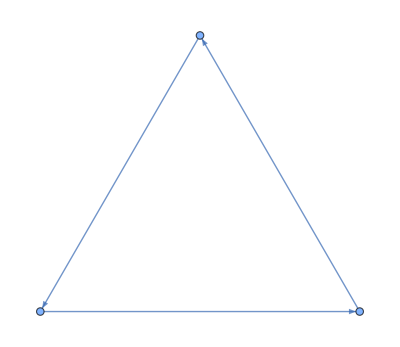

```mathematica
(* 21.1 *) Graph[{1->2,2->3,3->1}]
```

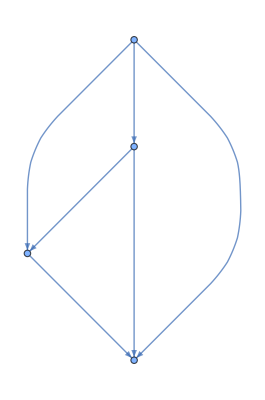

```mathematica
(* 21.2 *) Graph[{1->2,1->3,1->4,2->3,2->4,3->4}]
```

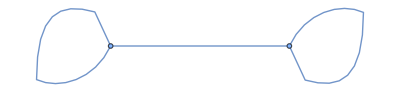
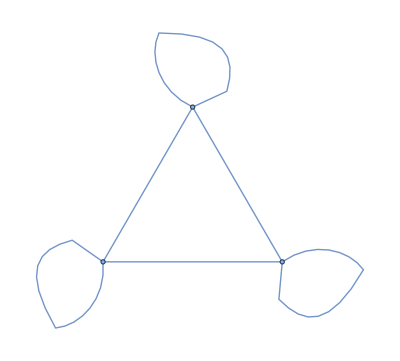
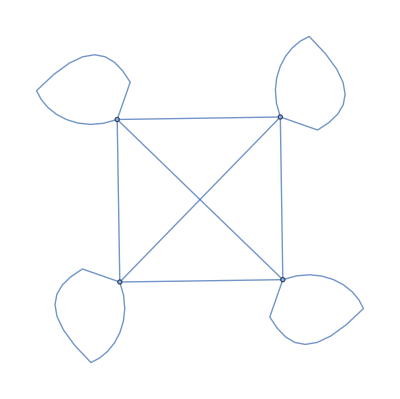
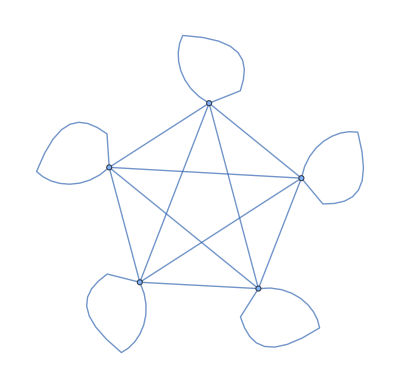
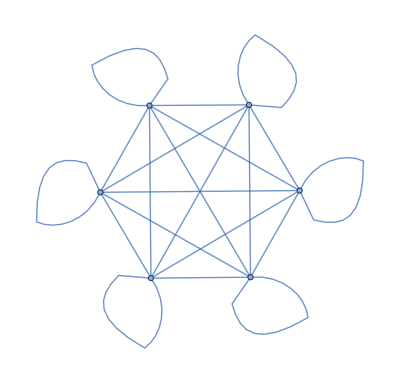
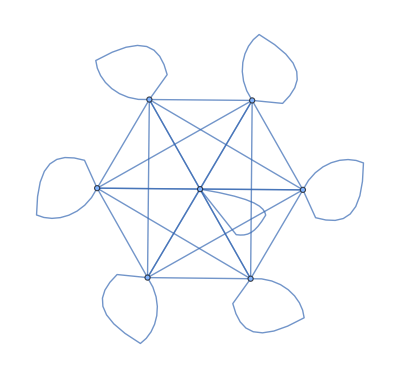
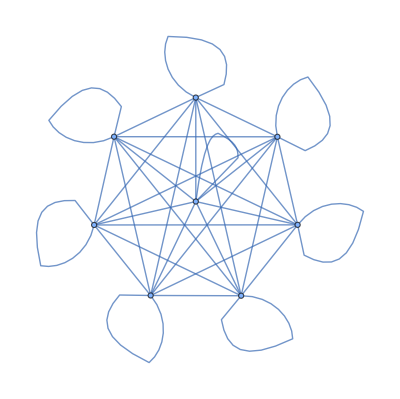
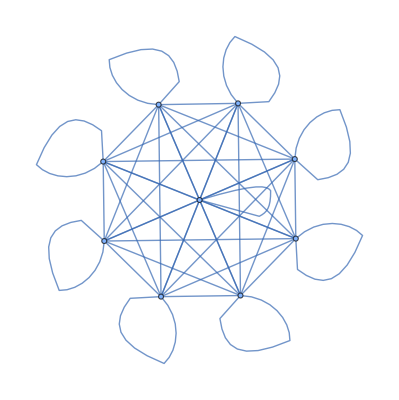

```mathematica
(* 21.3 *) Table[UndirectedGraph[Flatten[Table[i->j,{i,nodes},{j,nodes}]]],{nodes,2,10}]
```

```mathematica
(* 21.4 *) Flatten[Table[i,3,{i,2}]]
```

{1,2,1,2,1,2}

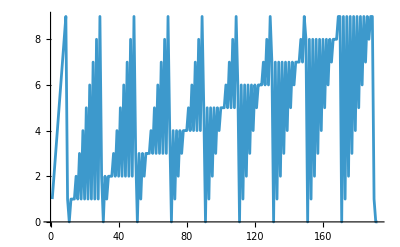

```mathematica
(* 21.5 *) ListLinePlot[Flatten[Table[IntegerDigits[number],{number, 100}]]]
```

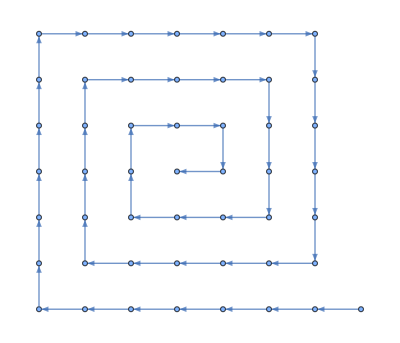

```mathematica
(* 21.6 *) Graph[Table[i->i+1,{i,1,49}]]
```

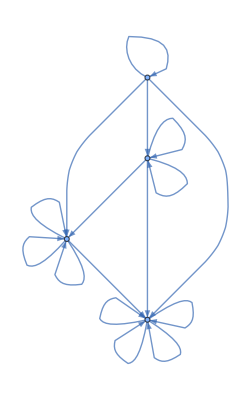

```mathematica
(* 21.7 *) Graph[Flatten[Table[i->Max[i,j],{i,4},{j,4}]]]
```

```mathematica
(* 21.8 *) Graph[Flatten[Table[i->j-i,{i,5},{j,5}]]]
```

-Graphics-

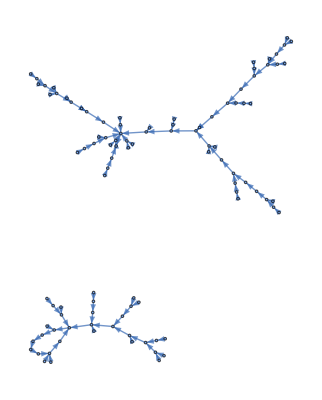

```mathematica
(* 21.9 *) Graph[Table[i->RandomInteger[{1,100}],{i,100}]]
```

```mathematica
(* 21.10 *) Graph[Flatten[Table[{i->RandomInteger[{1,100}],i->RandomInteger[{1,100}]},{i,100}]]]
```

-Graphics-

```mathematica
(* 21.11 *) Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],i,j],{i,4},{j,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

## Exercises from EIWL3 Section 22

```mathematica
(* 22.1 *) LanguageIdentify["ajatella"]
```

Finnish

```mathematica
(* This will be useful in the next two exercises: *)
tigerImage=Entity["TaxonomicSpecies","PantheraTigris::63rj9"][EntityProperty["TaxonomicSpecies","Image"]];
```

```mathematica
(* 22.2 *) ImageIdentify[tigerImage]
```

Import::filecorr: File is corrupt or is not a WLNet file.

NetModel::modelcorrupt: Cached version of model "Wolfram ImageIdentify Net V2" appears to be corrupt. Remove the downloaded files using DeleteObject[ResourceObject[Wolfram ImageIdentify Net V2]] and try again.

ImageIdentify::wlnetcorr: A required WLNet file is corrupted and could not be loaded.

$Failed

```mathematica
(* 22.3 *) 
ImageIdentify[Table[Blur[tigerImage,blur],{blur,5}]]
```

ImageIdentify::wlnetcorr: A required WLNet file is corrupted and could not be loaded.

$Failed

```mathematica
(* 22.4 *) Classify["Sentiment", "I'm so happy to be here"]
```

Positive

```mathematica
(* 22.5 *) Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
(* 22.6 *) Nearest[RandomInteger[1000,20],100,3]
```

{145,26,176}

```mathematica
(* 22.7 *) Nearest[RandomColor[10],Red,5]
```

{RGBColor[0.8465917950001807, 0.37438188541628636, 0.2653058731493525],RGBColor[0.9147123418911702, 0.5872223284183256, 0.5112086671068772],RGBColor[0.6239026872419666, 0.454693974632705, 0.14720949346430556],RGBColor[0.3494761085723441, 0.09678568083010863, 0.0055280467758895835],RGBColor[0.9821046470752861, 0.8303735279665994, 0.6778858828092313]}

```mathematica
(* 22.8 *) Nearest[Range[100]^2,2000]
```

{2025}

```mathematica
(* 22.9 *) Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

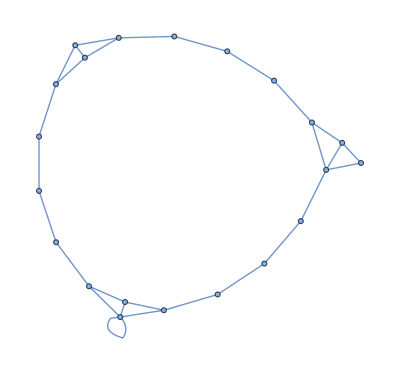

```mathematica
(* 22.10 *) NearestNeighborGraph[Table[Hue[h],{h,0,1,0.05}],2]
```

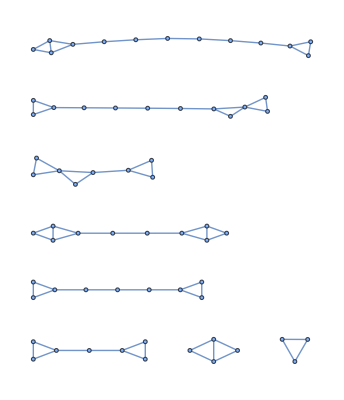

```mathematica
(* 22.11 *) NearestNeighborGraph[RandomInteger[100,100],2]
```


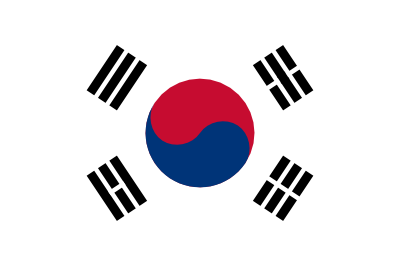
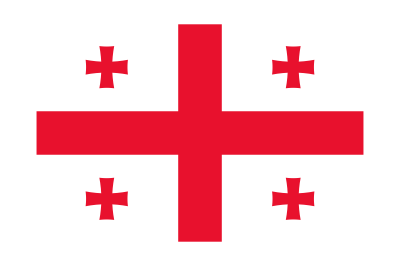
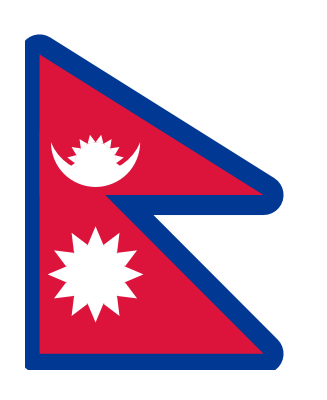
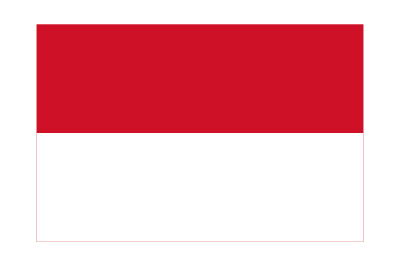
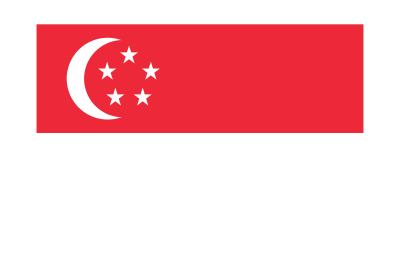
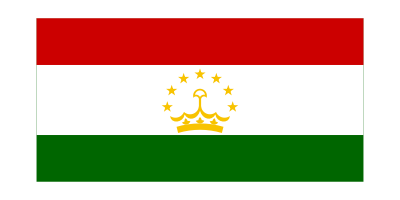
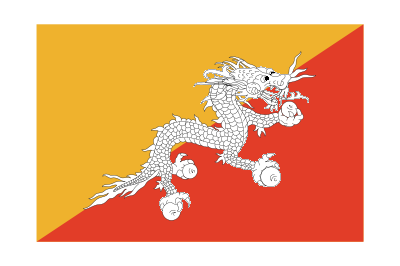
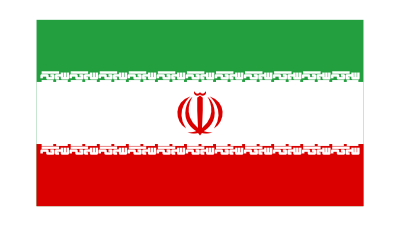

{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
(* 22.12 *) FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]]
```

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
(* 22.13 *) Table[Rasterize[letter,RasterSize->20],{letter,Alphabet[]}]
```

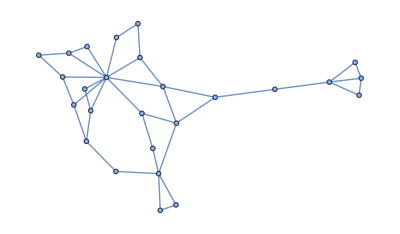

```mathematica
NearestNeighborGraph[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]
```